```mathematica
vmaxVals={0,0.01,0.05,0.1,0.5,5,10}
```

{0,0.01,0.05,0.1,0.5,5,10}

```mathematica
data2d=#[[All,1;;2]]&/@(Import[NotebookDirectory[]<>"vmax/"<>ToString[#]]&/@vmaxVals)
```

```mathematica
data3d=MapIndexed[Insert[#1,vmaxVals[[#2[[1]]]],1]&,data2d,{2}]
```

```mathematica
Flatten[data3d,1]
```

```mathematica
Show[ListPointPlot3D[#,ScalingFunctions->{"Log",None,None}]]&@Flatten[data3d,1]
```

-Graphics3D-

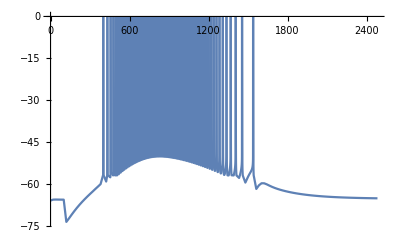

```mathematica
ListPlot[data2d[[3]],Joined->True]
```

```mathematica
graphData[filename_]:=Module[
{data2d=#[[1;;2]]&/@(Import[NotebookDirectory[]<>ToString[filename]])},
ListPlot[#,Joined->True]&@data2d
]
```

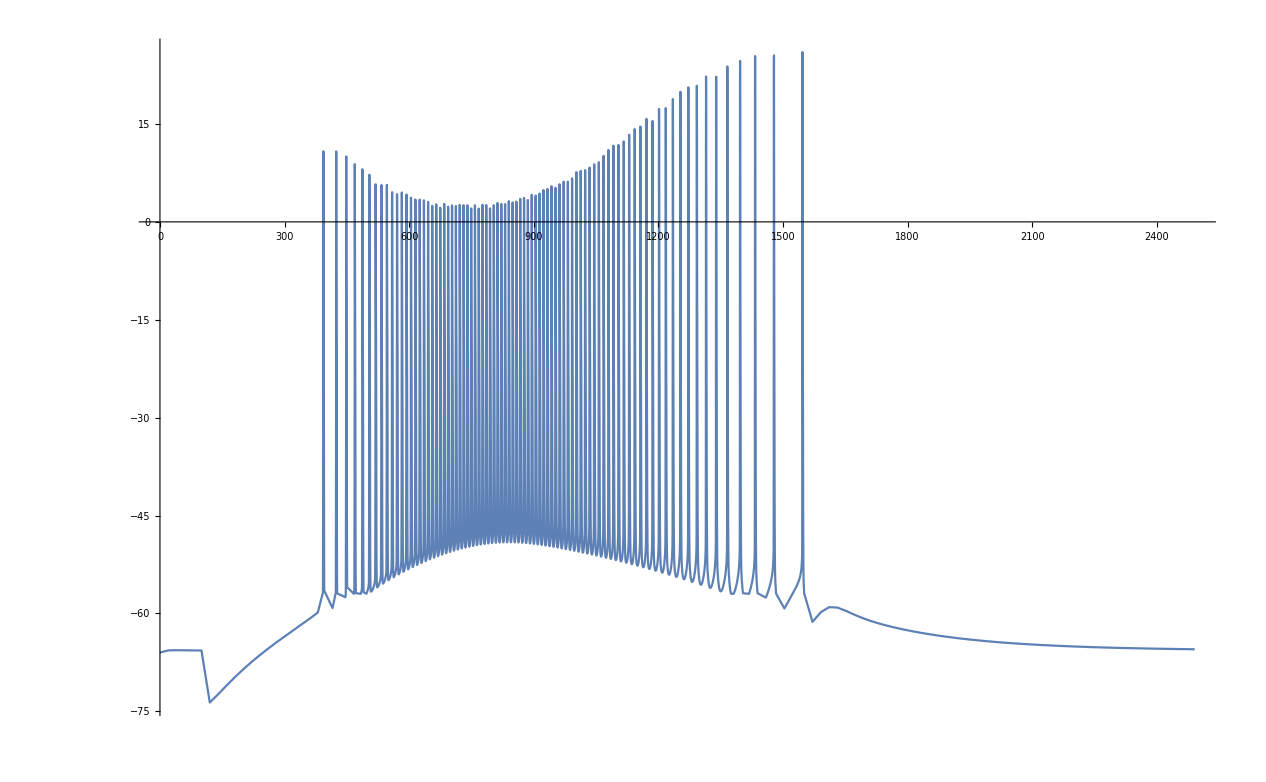

```mathematica
graphData["vmax/0"]
```